```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/johann/Dropbox/projects/approximation

## GSL

If the GNU Scientific Library is compiled, we can call its  function from Mathematica:

```mathematica
gslSin=ForeignFunctionLoad["/usr/local/lib/libgsl","gsl_sf_sin",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

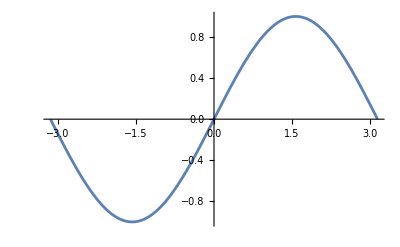

```mathematica
Plot[gslSin[x],{x,-3.14,3.14}]
```

It’s accurate to machine precision, or pretty close.

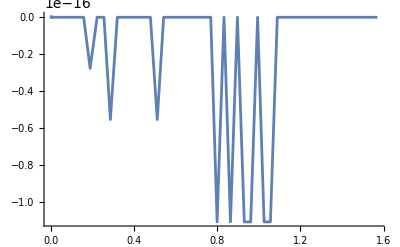

```mathematica
Plot[gslSin[x]-Sin[x],{x,0,Pi/2},WorkingPrecision->24,
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

Even at large arguments:

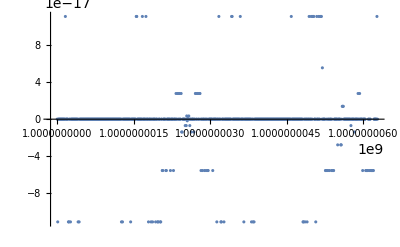

```mathematica
ListPlot[Table[{x,gslSin[x]-Sin[x]},{x,10^9,10^9+2π,0.01}]]
```

```mathematica
Max[Table[Abs[gslSin[x]-Sin[x]],{x,10^9,10^9+2π,0.01}]]
```

1.11022×10^-16

This is the source for the GSL  function:

```mathematica
int
gsl_sf_sin_e(double x, gsl_sf_result * result)
{
  /* CHECK_POINTER(result) */

  {
    const double P1 = 7.85398125648498535156e-1;
    const double P2 = 3.77489470793079817668e-8;
    const double P3 = 2.69515142907905952645e-15;

    const double sgn_x = GSL_SIGN(x);
    const double abs_x = fabs(x);

    if(abs_x < GSL_ROOT4_DBL_EPSILON) {
      const double x2 = x*x;
      result->val = x * (1.0 - x2/6.0);
      result->err = fabs(x*x2*x2 / 100.0);
      return GSL_SUCCESS;
    }
    else {
      double sgn_result = sgn_x;
      double y = floor(abs_x/(0.25*M_PI));
      int octant = y - ldexp(floor(ldexp(y,-3)),3);
      int stat_cs;
      double z;

      if(GSL_IS_ODD(octant)) {
        octant += 1;
        octant &= 07;
        y += 1.0;
      }

      if(octant > 3) {
        octant -= 4;
        sgn_result = -sgn_result;
      }
      
      z = ((abs_x - y * P1) - y * P2) - y * P3;

      if(octant == 0) {
        gsl_sf_result sin_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&sin_cs, t, &sin_cs_result);
        result->val = z * (1.0 + z*z * sin_cs_result.val);
      }
      else { /* octant == 2 */
        gsl_sf_result cos_cs_result;
        const double t = 8.0*fabs(z)/M_PI - 1.0;
        stat_cs = cheb_eval_e(&cos_cs, t, &cos_cs_result);
        result->val = 1.0 - 0.5*z*z * (1.0 - z*z * cos_cs_result.val);
      }

      result->val *= sgn_result;

      if(abs_x > 1.0/GSL_DBL_EPSILON) {
        result->err = fabs(result->val);
      }
      else if(abs_x > 100.0/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * abs_x * GSL_DBL_EPSILON * fabs(result->val);
      }
      else if(abs_x > 0.1/GSL_SQRT_DBL_EPSILON) {
        result->err = 2.0 * GSL_SQRT_DBL_EPSILON * fabs(result->val);
      }
      else {
        result->err = 2.0 * GSL_DBL_EPSILON * fabs(result->val);
      }

      return stat_cs;
    }
  }
}
```

### GSL Angle Reduction

#### Mathematica Version

I’ll try to reproduce the angle-reduction algorithm from the GSL Sin function in Mathematica.

```mathematica
Clear[gslY,gslZ,gslT,ldexp,octant]
```

```mathematica
gslY[x_]:= Floor[Abs[x]/(π/4)]
```

```mathematica
ldexp[x_,c_]:=x*2^c;
```

```mathematica
octant[x_]:=With[{y=gslY[x]},
y - ldexp[Floor[ldexp[y,-3]],3] 
]
```

```mathematica
gslZ[x_]:=With[{
P1= 7.85398125648498535156*10^-1,
P2= 3.77489470793079817668*10^-8,
P3= 2.69515142907905952645*10^-15,
y = gslY[x]},
(*((Abs[x] - y * P1) - y * P2) - y * P3]*)
result=Abs[x];
result-=y*P1;
result-=y*P2;
result-=y*P3;
result]
```

```mathematica
gslT[x_]:=8/π*Abs[gslZ[x]] - 1
```

Y gives the integer number of multiples of π/4 < x, and octant reduces that number mod 8:

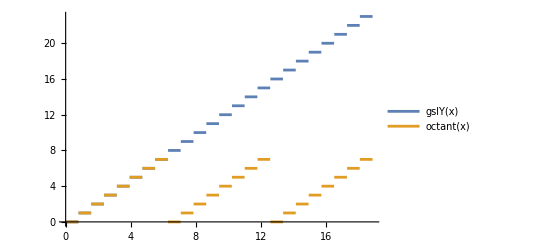

```mathematica
Plot[{gslY[x],octant[x]},{x,0,6Pi},PlotLegends->"Expressions"]
```

P1, P2 & P3 add up to π/4:

```mathematica
P1= 7.85398125648498535156*10^-1;
P2= 3.77489470793079817668*10^-8;
P3= 2.69515142907905952645*10^-15;
TableForm[Transpose[{{"P1","P2","P3","P1+P2+P3","π/4"},{DecimalForm[P1,DigitBlock->5],DecimalForm[P2,DigitBlock->5],DecimalForm[P3,DigitBlock->5],DecimalForm[N[P1+P2+P3,34],DigitBlock->5],DecimalForm[N[Pi/4,34],DigitBlock->5]}}]]
```

P1 | 0.78539 81256 48498 53516
P2 | 0.00000 00377 48947 07930 79817 67
P3 | 0.00000 00000 00002 69515 14290 79059 5264
P1+P2+P3 | 0.78539 81633 97448 30962
π/4 | 0.78539 81633 97448 30961 56608 45819 8757

Z gives :

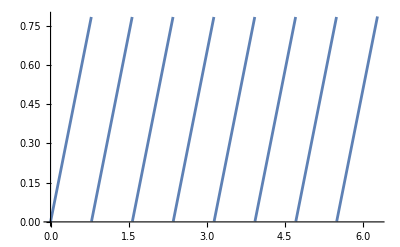

```mathematica
Plot[gslZ[x],{x,0,2Pi}]
```

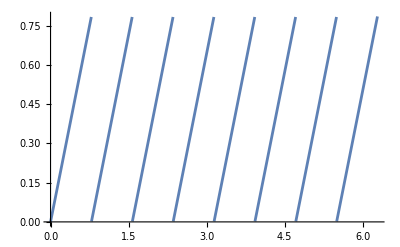

```mathematica
Plot[Mod[x,Pi/4],{x,0,2Pi}]
```

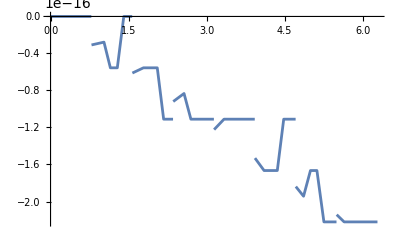

```mathematica
Plot[gslZ[x]-Mod[x,Pi/4],{x,0,2Pi}]
```

But at large arguments appears to be off quite a bit:

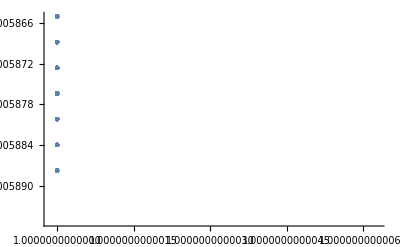

```mathematica
ListPlot[
Table[
{x,gslZ[x]-Mod[x,Pi/4]},{x,10^12,10^12+2Pi,0.01}]
]
```

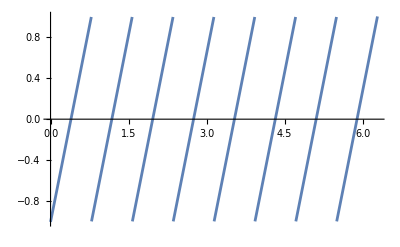

```mathematica
Plot[gslT[x],{x,0,2Pi}]
```

```mathematica
gslReduce[x_]:=N[(gslT[x]+1)*π/8,50]
```

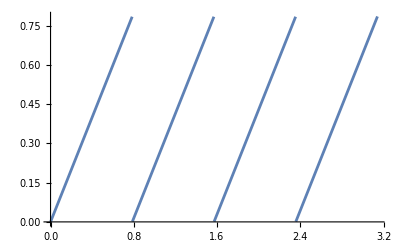

```mathematica
Plot[gslReduce[x],{x,0,π}]
```

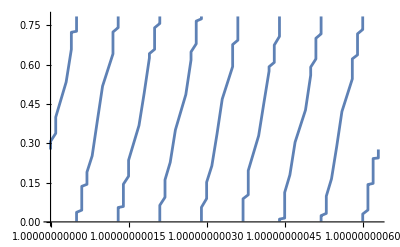

```mathematica
Plot[gslReduce[x],{x,10^10,2π+10^10}]
```

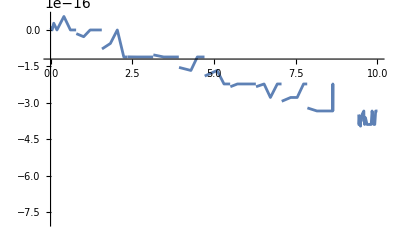

```mathematica
Plot[gslReduce[x]-Mod[x,π/4],{x,0,10}]
```

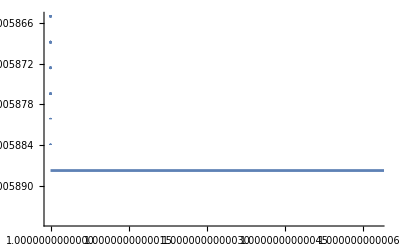

```mathematica
Plot[gslReduce[x]-N[Mod[x,π/4],24],{x,10^12,2π+10^12}]
```

Why is the error in this so large?

#### C Version

My version of the angle-reduction logic from GSL Sin, as a separate C function.

```mathematica
CellPrint[Cell[Import["/Users/johann/Dropbox/projects/approximation/sin/angle_reduction.c","Text"],"Code"]]
```

```mathematica
#include <gsl/gsl_math.h>

// This extracts the angle-reduction logic from
// gsl_sf_sin in the specfunc/trig.c file from GSL.

double gslReduceBase(double x) {
  const double P1 = 7.85398125648498535156e-1;
  const double P2 = 3.77489470793079817668e-8;
  const double P3 = 2.69515142907905952645e-15;

  const double abs_x = fabs(x);

  double y = floor(abs_x / (0.25 * M_PI));
  double z = ((abs_x - y * P1) - y * P2) - y * P3;
  double t = 8.0 * fabs(z) / M_PI - 1.0;

  return t;
}

// The function gslReducebase maps each octant
// onto [-1, +1].  So scale it to [0, Pi/4].

double gslReduce(double x) {
  double y = gslReduceBase(x);
  y = (y + 1)*M_PI_4/2;
  return y;
}
```

```mathematica
gslReduceExt=ForeignFunctionLoad["./sin/libmysin","gslReduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

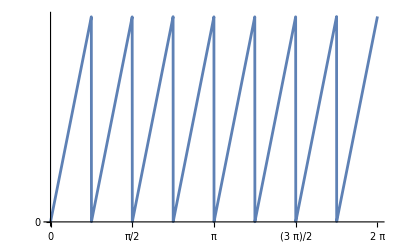

```mathematica
Plot[gslReduceExt[x],{x,0,2Pi},Ticks->{Table[n*Pi/4,{n,0,8}],{-1,0,1}}]
```

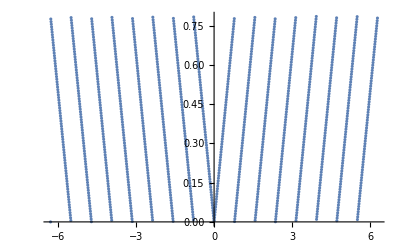

```mathematica
ListPlot[Table[{x,gslReduceExt[x]},{x,-2Pi,2Pi,0.01}]]
```

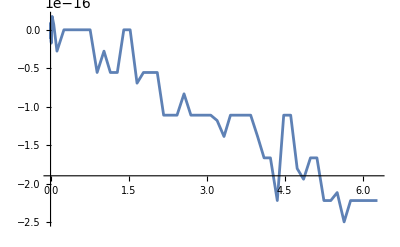

```mathematica
Plot[gslReduceExt[x]-N[Mod[x,π/4],24],{x,0,2π}]
```

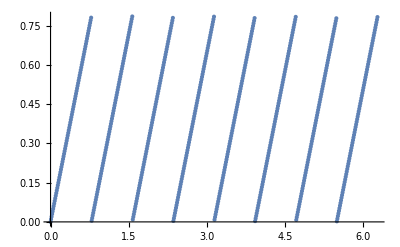

```mathematica
ListPlot[
Table[{x,gslReduceExt[x]},{x,0,2π,0.01}]
]
```

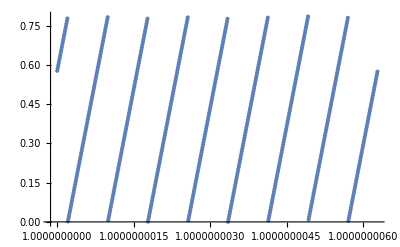

```mathematica
ListPlot[
Table[{x,gslReduceExt[x]},{x,10^9,2π+10^9,0.01}]
]
```

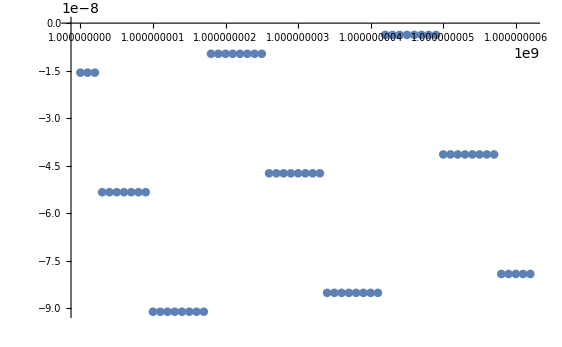

```mathematica
ListPlot[
Table[{x,gslReduceExt[x]-N[Mod[x,π/4]]},{x,10^9,2π+10^9,0.1}]
]
```

```mathematica
$MaxExtraPrecision=200;
disp[x_]:=DecimalForm[x,{18,17},DigitBlock->3,NumberSeparator->" "]
x=N[2π+10^12];
a=gslReduceExt[x];
b=Mod[x,π/4];
d=a-b;
{
disp[N[a,24]],
disp[N[b,24]]
}//TableForm
disp[N[d,24]]
```

0.127 791 222 081 075 40
0.127 807 617 187 500000

-0.000 016 395 106 424 62

```mathematica
{#,Precision[Symbol[#]],Accuracy[Symbol[#]]}&/@{"a","b","d"}//TableForm
```

a | MachinePrecision | 16.8481
b | MachinePrecision | 16.848
d | MachinePrecision | 20.7399

### GSL Chebyshev Approximation

```mathematica
/* Chebyshev expansion for f(t) = g((t+1)Pi/8), -1<t<1
 * g(x) = (sin(x)/x - 1)/(x*x)
 */
static double sin_data[12] = {
  -0.3295190160663511504173,
   0.0025374284671667991990,
   0.0006261928782647355874,
  -4.6495547521854042157541e-06,
  -5.6917531549379706526677e-07,
   3.7283335140973803627866e-09,
   3.0267376484747473727186e-10,
  -1.7400875016436622322022e-12,
  -1.0554678305790849834462e-13,
   5.3701981409132410797062e-16,
   2.5984137983099020336115e-17,
  -1.1821555255364833468288e-19
};
static cheb_series sin_cs = {
  sin_data,
  11,
  -1, 1,
  11
};

/* Chebyshev expansion for f(t) = g((t+1)Pi/8), -1<t<1
 * g(x) = (2(cos(x) - 1)/(x^2) + 1) / x^2
 */
static double cos_data[11] = {
  0.165391825637921473505668118136,
 -0.00084852883845000173671196530195,
 -0.000210086507222940730213625768083,
  1.16582269619760204299639757584e-6,
  1.43319375856259870334412701165e-7,
 -7.4770883429007141617951330184e-10,
 -6.0969994944584252706997438007e-11,
  2.90748249201909353949854872638e-13,
  1.77126739876261435667156490461e-14,
 -7.6896421502815579078577263149e-17,
 -3.7363121133079412079201377318e-18
};
static cheb_series cos_cs = {
  cos_data,
  10,
  -1, 1,
  10
};
```

```mathematica
t[x_]:=π/8(x+1)
```

```mathematica
f[t_]:=(Sin[t]/t-1)/t^2
```

```mathematica
g[t_]:=(2(Cos[t]-1)/t^2+1)/t^2
```

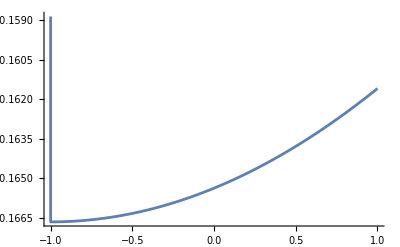

```mathematica
Plot[f[t[x]],{x,-1,1}]
```

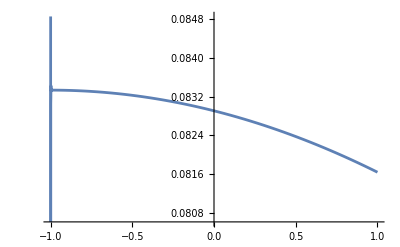

```mathematica
Plot[g[t[x]],{x,-1,1}]
```

## Calling Assembly Language

### sin1.s

This is the most basic approximation, using just the first two terms of the Taylor series, as a proof that we can write a dynamic library in ARM assembly and call it from C and from Mathematica.

```mathematica
CellPrint[Cell[Import["sin/sin1.s","Text"],"Code"]]
```

```mathematica
// sin1.s
// Approximate Sin(x) by the Taylor series to degree 3.

.global _sin_1
.p2align 2			// Make sure everything is aligned properly

.text

_sin_1:
        fmul    d1, d0, d0              // d1 = d0^2
        fmul    d1, d1, d0              // d1 = d0^3
        fmov    d2, #6
        fdiv    d1, d1, d2              // d1 = d0^3/6
        fsub    d0, d0, d1              // d0 = d0 - d0^3/6
        ret
```

```mathematica
sin1=ForeignFunctionLoad["./sin/libmysin","sin_1",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

```mathematica
sin1[0]
```

0.

```mathematica
sin1[N[Pi/2]]
```

0.924832

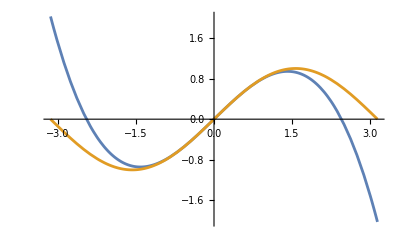

```mathematica
Plot[{sin1[x],Sin[x]},{x,-Pi,Pi}]
```

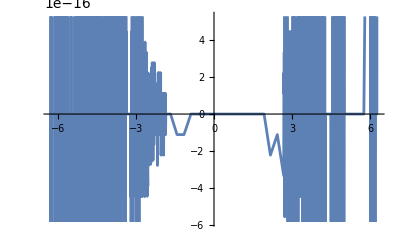

```mathematica
Plot[sin1[x]-(x-x^3/6),{x,-2π,2π},WorkingPrecision->24]
```

### sin2.s

```mathematica
This is a Chebyshev approximation to Sin, without any angle reduction.
```

```mathematica
CellPrint[Cell[Import["sin/sin2.s","Text"],"Code"]]
```

```mathematica
// sin2.s
// Approximate Sin(x) by Chebyshev approximation

.global         _sin_2
.p2align        2			// Make sure everything is aligned properly

        .macro  LOADVAL reg, name
        adrp    x0, \name@GOTPAGE
        ldr     x0, [x0, \name@GOTPAGEOFF]
        ldr     \reg, [x0]
        .endm

.text

_sin_2:
        LOADVAL d1, a0
        LOADVAL d2, a1
        LOADVAL d3, a2
        LOADVAL d4, a3
        LOADVAL d5, a4
        LOADVAL d6, a5
        LOADVAL d7, a6
        LOADVAL d8, a7
        LOADVAL d9, a8
        LOADVAL d10, a9
        LOADVAL d11, a10
        LOADVAL d12, a11
        LOADVAL d13, a12
        LOADVAL d14, a13

        fmadd   d13, d14, d0, d13
        fmadd   d12, d13, d0, d12
        fmadd   d11, d12, d0, d11
        fmadd   d10, d11, d0, d10
        fmadd   d9, d10, d0, d9
        fmadd   d8, d9, d0, d8
        fmadd   d7, d8, d0, d7
        fmadd   d6, d7, d0, d6
        fmadd   d5, d6, d0, d5
        fmadd   d4, d5, d0, d4
        fmadd   d3, d4, d0, d3
        fmadd   d2, d3, d0, d2
        fmadd   d1, d2, d0, d1

        fmov    d0, d1
        ret

.p2align        2
.data
a0:	.double	+3.15159609307366933583264e-17
a1:	.double	+9.99999999999992137463981e-1
a2:	.double	+3.24848403977218879514298e-13
a3:	.double	-1.66666666671945646405887e-1
a4:	.double	+4.46929940061919965152147e-11
a5:	.double	+8.33333310712103651500584e-3
a6:	.double	+7.39903364746182917886826e-10
a7:	.double	-1.98414335571346275936300e-4
a8:	.double	+2.51241790401253696723421e-9
a9:	.double	+2.75303544969185019022074e-6
a10:	.double	+2.00650971121911487700779e-9
a11:	.double	-2.60546344930653900663444e-8
a12:	.double	+3.11243537080303902068867e-10
a13:	.double	+1.12392760716968552199773e-10
```

```mathematica
Clear[sin2]
sin2=ForeignFunctionLoad["./sin/libmysin","sin_2",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

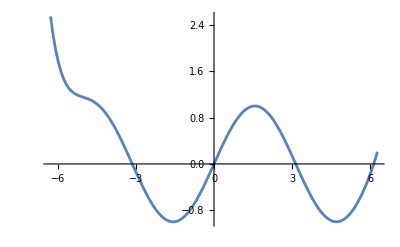

```mathematica
Plot[sin2[x],{x,-2Pi,2Pi}]
```

### sin3.s

```mathematica
CellPrint[Cell[Import["sin/sin3.s","Text"],"Code"]]
```

```mathematica
// sin2.s
// Approximate Sin(x) by Chebyshev approximation

.global         _sin_3
.p2align        2		// Make sure everything is aligned properly

        .macro  LOADVAL reg, name
        adrp    x0, \name@GOTPAGE
        ldr     x0, [x0, \name@GOTPAGEOFF]
        ldr     \reg, [x0]
        .endm

.text

_sin_3:
        mov     w1, wzr         // we're going to use w1 to keep some flags
        fmov    d4, #2          // we're going to mulitply & divide by 2 later

        fcmp    d0, #0.0
        bge     pos             // x < 0, return -Sin(-x)
        mov     w1, 0x0001      // 1 in w1 bit 1 will mean negate the result at the end
        fneg    d0, d0

pos:
        LOADVAL d1, c2Pi        // d1 = 2*Pi
        fcmp    d0, d1
        ble     inrange
        fdiv    d3, d0, d1      // d0 > 2*Pi
        frintz  d3, d3          // floor
        fmsub   d0, d3, d1, d0

inrange:                        // d0 < 2*Pi
        fdiv    d1, d1, d4      // d1 = Pi
        fcmp    d0, d1
        ble     first_half      // 0 <= x <= Pi
        fsub    d0, d0, d1      // d0 = d0 - Pi
        eor     w1, w1, 0x0001  // toggle 1st bit of w1, to negate the final answer

first_half:
        fdiv    d1, d1, d4      // d1 = Pi/2
        fcmp    d0, d1
        ble     approx          // 0 <= d0 <= Pi/2 - calculate the approximation
        // Pi/2 < d0 <= Pi - return Sin(Pi-x)
        fmul    d1, d1, d4      // d1 = Pi
        fsub    d0, d1, d0      // d0 = Pi - d0

approx:
        LOADVAL d1, a0
        LOADVAL d2, a1
        LOADVAL d3, a2
        LOADVAL d4, a3
        LOADVAL d5, a4
        LOADVAL d6, a5
        LOADVAL d7, a6
        LOADVAL d8, a7
        LOADVAL d9, a8
        LOADVAL d10, a9
        LOADVAL d11, a10
        LOADVAL d12, a11
        LOADVAL d13, a12
        LOADVAL d14, a13

        fmadd   d13, d14, d0, d13
        fmadd   d12, d13, d0, d12
        fmadd   d11, d12, d0, d11
        fmadd   d10, d11, d0, d10
        fmadd   d9, d10, d0, d9
        fmadd   d8, d9, d0, d8
        fmadd   d7, d8, d0, d7
        fmadd   d6, d7, d0, d6
        fmadd   d5, d6, d0, d5
        fmadd   d4, d5, d0, d4
        fmadd   d3, d4, d0, d3
        fmadd   d2, d3, d0, d2
        fmadd   d1, d2, d0, d1

        fmov    d0, d1
        and     w1, w1, 0x0001
        cmp     w1, #0
        beq     end
        fneg    d0, d0

end:
        ret

.p2align        2
.data
a0:	.double	+3.15159609307366933583264e-17
a1:	.double	+9.99999999999992137463981e-1
a2:	.double	+3.24848403977218879514298e-13
a3:	.double	-1.66666666671945646405887e-1
a4:	.double	+4.46929940061919965152147e-11
a5:	.double	+8.33333310712103651500584e-3
a6:	.double	+7.39903364746182917886826e-10
a7:	.double	-1.98414335571346275936300e-4
a8:	.double	+2.51241790401253696723421e-9
a9:	.double	+2.75303544969185019022074e-6
a10:	.double	+2.00650971121911487700779e-9
a11:	.double	-2.60546344930653900663444e-8
a12:	.double	+3.11243537080303902068867e-10
a13:	.double	+1.12392760716968552199773e-10

c2Pi:   .double +6.28318530717958647692529

        /*
Questions:
        Is there a simpler way to multiply & divide FP registers by 2?
        Simple way to keep a flag and negate a FP value conditional on the flag?
        */
```

```mathematica
Clear[sin3]
sin3=ForeignFunctionLoad["./sin/libmysin","sin_3",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

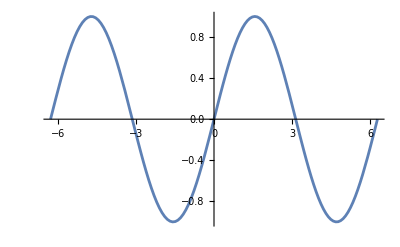

```mathematica
Plot[sin3[x],{x,-2Pi,2Pi}]
```

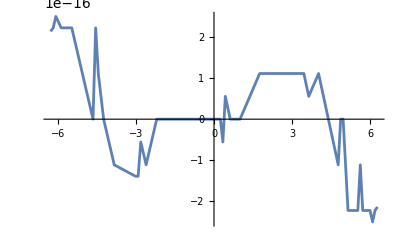

```mathematica
Plot[Sin[x]-sin3[x],{x,-2Pi,2Pi}]
```

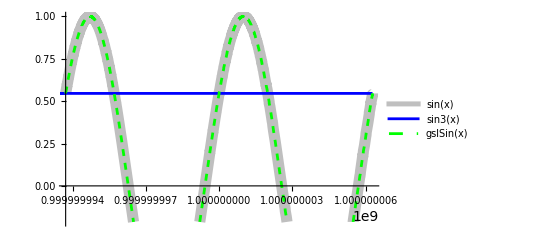

```mathematica
Plot[{Sin[x],sin3[x],gslSin[x]},{x,10^9-2Pi,10^9+2Pi},
PlotLegends->"Expressions",
MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}},
PlotStyle->{{Thickness[0.02],Opacity[0.5],Gray},{Blue},{Dashed,Green}}]
```

```mathematica
|
```

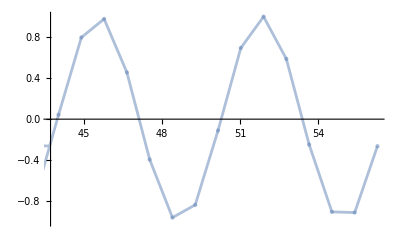

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

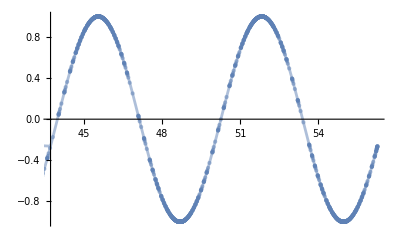

```mathematica
Plot[sin3[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]},MaxRecursion->15,
Method->{Refinement->{ControlValue->2°}}]
```

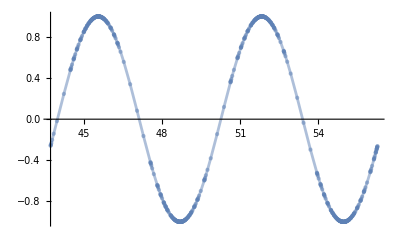

```mathematica
Plot[gslSin[x],{x,50-2Pi,50+2Pi},Mesh->All,PlotStyle->{Opacity[0.5]}]
```

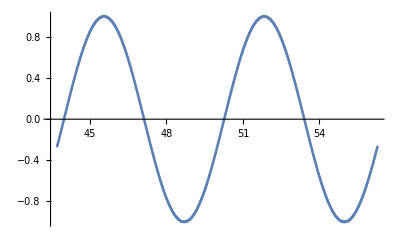

```mathematica
ListPlot[Table[{x,sin3[x]},{x,50-2Pi,50+2Pi,0.01}]]
```

```mathematica
reduce=ForeignFunctionLoad["./sin/libmysin","reduce",{"CDouble"}->"CDouble"]
```

ForeignFunction[…]

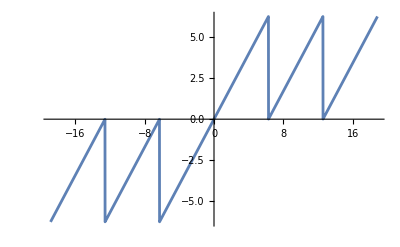

```mathematica
Plot[reduce[x],{x,-6Pi,6Pi}]
```

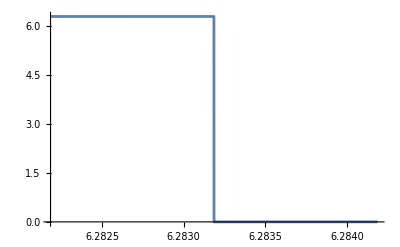

```mathematica
Plot[reduce[x],{x,2Pi-0.001,2Pi+0.001}]
```

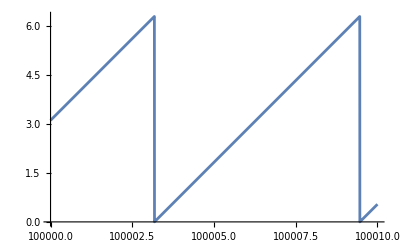

```mathematica
Plot[reduce[x],{x,100000,100010}]
```

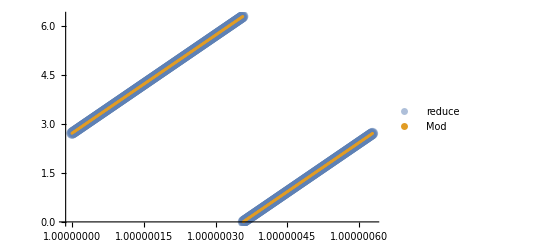

```mathematica
ListPlot[
{Table[{x,reduce[x]},{x,10000000,10000000+2Pi,0.01}],
Table[{x,N[Mod[x,2Pi],24]},{x,10000000,10000000+2Pi,0.01}]},
PlotLegends->{"reduce","Mod"},
PlotStyle->{{PointSize[0.02],Opacity[0.5]},{PointSize[0.005]}}
]
```

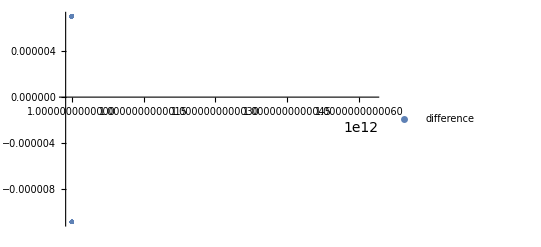

```mathematica
ListPlot[
Table[{x,reduce[x]-N[Mod[x,2Pi],18]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

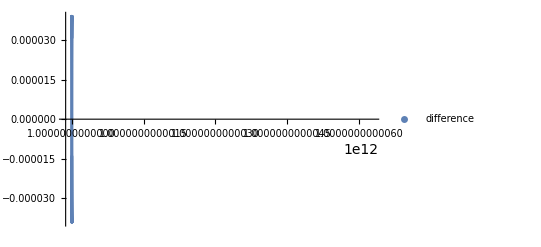

```mathematica
ListPlot[
Table[{x,sin3[x]-gslSin[x]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"difference"}]
```

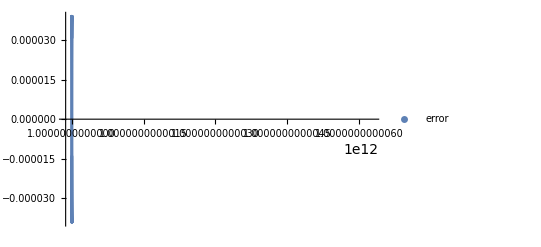

```mathematica
ListPlot[
Table[{x,sin3[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

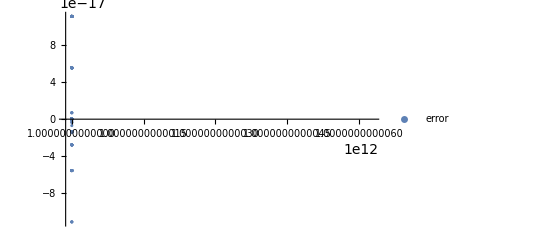

```mathematica
ListPlot[
Table[{x,gslSin[x]-N[Sin[x]]},{x,10^12,10^12+2Pi,0.01}],
PlotLegends->{"error"}]
```

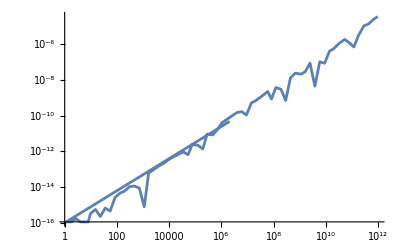

```mathematica
LogLogPlot[(Sin[#]-sin3[#]&)[x],{x,0, 10^12},PlotRange->All]
```

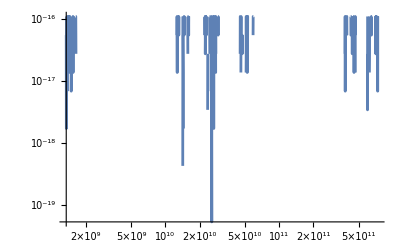

```mathematica
LogLogPlot[(Sin[#]-gslSin[#]&)[x],{x,0, 10^12},PlotRange->All]
```